```mathematica
M2=0.1*1.9891*10^30;
M1=0.73*1.9891*10^30;
m=M1/(M1+M2) 

LDOT=Solve[D[-(1-m)/(√((x+m)^2))-m/(√((x-(1-m))^2))-1/2 x^2,x]==0,x];
Pmax=((-(1-m)/(√((x+m)^2))-m/(√((x-(1-m))^2))-1/2 x^2)/.LDOT)//N
L=-x/.LDOT[[2]];
G=6.67430*10^-11;
```

0.879518

{-1.74747,-1.82547,-1.5599}

```mathematica
Show[ContourPlot3D[Evaluate[(-(1-m)/(√((x+m)^2+y^2+z^2))-m/(√((x-(1-m))^2+y^2+z^2))-1/2(x^2+y^2+z^2)==Pmax[[2]])/.{x->xx-m}],{xx,-0.3,1.5},{y,-0.6,0.6},{z,-0.6,0.6},AxesLabel->Automatic],
Graphics3D[{Directive[Red,PointSize[0.2]],Point[{l,0,0}]}]]
```

-Graphics3D-

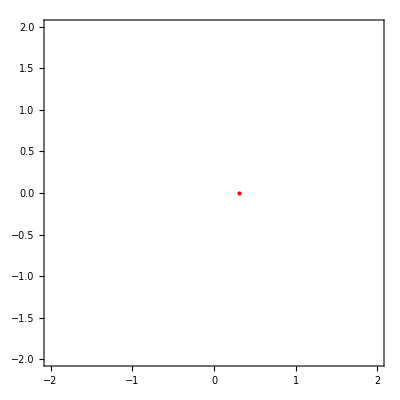

```mathematica
l=0.9;
Show[ContourPlot[-G M1/(√((x-L)^2+y^2))-G M2/(√((x+l)^2+y^2))-1/2((l)^2+L^2)==-G M2/l-1/2((l)^2+L^2)-G M1/L,{x,-2,2},{y,-2,2}],
Graphics[{Red,Point[{0.302,0}]}]]
```